```mathematica
Tf = 0.760148;tauf=6.35185;d=2;DD=0.16;
χ=(2/3)*Tf^2;
sf=9.1518;
m=0.707292;
```

```mathematica
Δξ = 18/100;
```

```mathematica
(2DD χ Tf)/(tauf sf^2 Δξ)1/(2*tauf)
```

0.000077026

```mathematica
w = √(8*0.162*(1/0.5-1/tauf))
```

1.5453

```mathematica
Qfactor=NIntegrate[1/Cosh[x]^2 Gamma[3,m/Tf Cosh[x]],{x,-Infinity,Infinity}]
```

3.33243

```mathematica
Fn[x_]:=1/(χ Cosh[x]^2)Gamma[3,m/Tf Cosh[x]]
```

```mathematica
Cnn[x1_,x2_]:=(χ Tf)/tauf   1/(√(π w^2))Exp[-(x1 - x2)^2/w^2]
```

```mathematica
B[y_]:= (d tauf Tf)/(4 π^2 Qfactor)NIntegrate[Fn[-ξ1]Fn[y-ξ2]Cnn[ξ1,ξ2],{ξ1,-10,10},{ξ2,-5,5}](*(d tauf Tf)/(4 π^2 Qfactor)*)
```

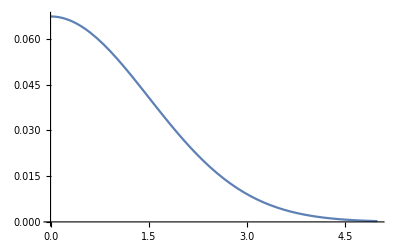

```mathematica
Plot[B[y],{y,0,5}]
```

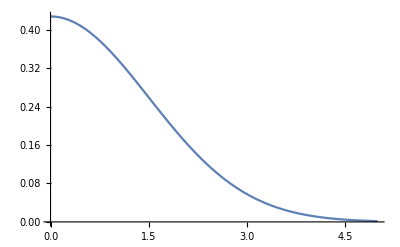

```mathematica
Plot[tauf B[y],{y,0,5}]
```

```mathematica
Balancedirac[y_]:=(d tauf Tf)/(4 π^2 Qfactor)(χ Tf)/tauf NIntegrate[Fn[-ξ1]Fn[y-ξ1],{ξ1,-10,10}]
```

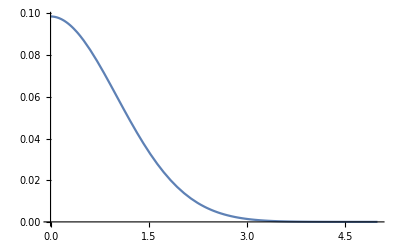

```mathematica
Plot[Balancedirac[y],{y,0,5}]
```

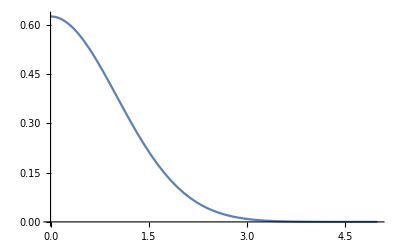

```mathematica
Plot[tauf Balancedirac[y],{y,0,5}]
```

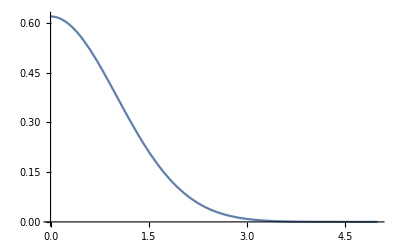

```mathematica
Plot[2π Balancedirac[y],{y,0,5}]
```

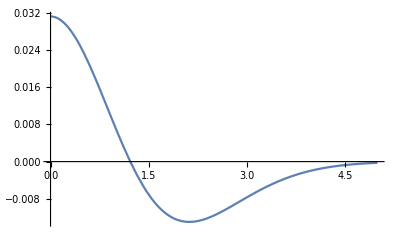

```mathematica
Plot[Balancedirac[y]-B[y],{y,0,5}]
```

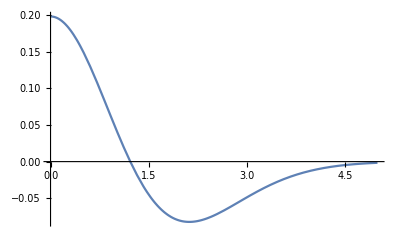

```mathematica
Plot[tauf*(Balancedirac[y]-B[y]),{y,0,5}]
```

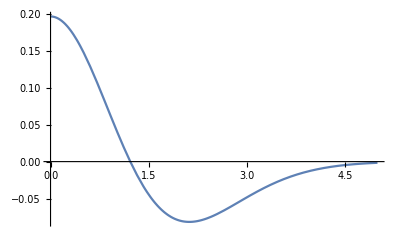

```mathematica
Plot[2π(Balancedirac[y]-B[y]),{y,0,5}]
```

```mathematica
(*Integration Checks*)
```

```mathematica
NIntegrate[Balancedirac[dy]-B[dy],{dy,0,5}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.

```mathematica
NIntegrate[0.0169Exp[(-Abs[x-y]^2)/1.55^2],{x,-4.5,4.5},{y,-4.5,4.5}]
```

0.377263

```mathematica
NIntegrate[0.0169Exp[(-Abs[x-y]^2)/1.55^2],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.39288

```mathematica
NIntegrate[0.0169Exp[(-Abs[x-y]^2)/1.55^2],{x,-4.5,4.5},{y,-4.5,4.5}]
```

0.377263

```mathematica
NIntegrate[0.0169Exp[(-(x-y)^2)/1.55^2],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.39288

```mathematica
NIntegrate[0.0169Exp[(-(x-y)^2)/1.55^2],{x,-4.5,4.5},{y,-4.5,4.5}]
```

0.377263

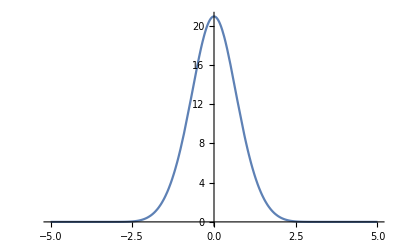

```mathematica
Plot[NIntegrate[Fn[-ξ1]Fn[y-0],{y,0,10}],{ξ1,-5,5}]
```

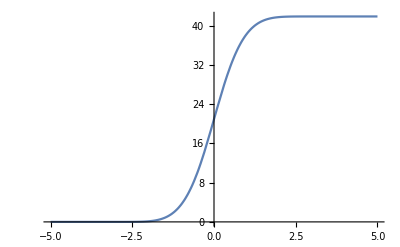

```mathematica
Plot[NIntegrate[Fn[0]Fn[y-ξ2],{y,0,10}],{ξ2,-5,5}]
```

```mathematica
tauQ = 0.053;
```

```mathematica
tauQ/tauf
```

0.00834403

```mathematica
NIntegrate[Exp[(-(tauf-x))/tauQ] 1/x,{x,0.5,tauf}]
```

0.00841484

```mathematica
NIntegrate[Exp[(-(tauf-x))/tauQ],{x,0.5,tauf}]
```

0.053

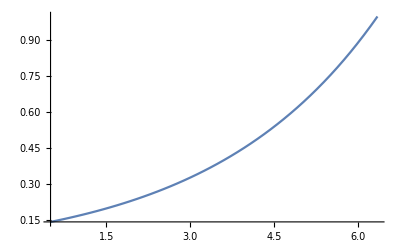

```mathematica
Plot[Exp[(-(tauf-x))/3],{x,0.5,tauf}]
```